```mathematica
ClearAll["Global`*"];
```

```mathematica
cutOff=150; (*number of coefficients a[n] kept in the sums*)
γ=4; (* value of the interactions*)
Do[a[r]=N[1/(2*π^2*r)(1-(-1)^r)],{r,1,cutOff}]; (*initialization*)
Do[aNew[r]=a[r],{r,1,cutOff}]; (*initialization*)
Do[f[n,r]=If[n==r,N[((32*r^2)/(1-4*r^2))],If[(-1)^(n+r)==-1,0,N[(16*n*r*(1+(-1)^(n+r)))/(n^4-2*n^2(r^2+1)+(r^2-1)^2)]]];
,{n,1,cutOff},{r,1,cutOff}];
```

```mathematica
numIterations=400;
Do[
Do[aNew[r]=1/(2*π^2*r)(1-(-1)^r)+1/(γ*r*π)Sum[a[n]*f[n,r],{n,1,cutOff}],{r,1,cutOff}];
Do[a[r]=aNew[r];,{r,1,cutOff}];
,{s,1,numIterations}];
```

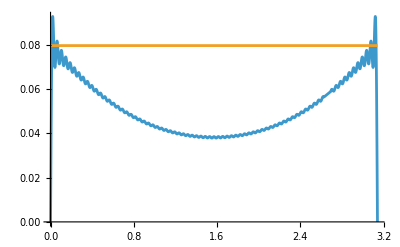

```mathematica
Plot[{Sum[aNew[n]*Sin[n*x],{n,1,cutOff}],1/(4*π)},{x,0,π},PlotRange->All]
```